# Notebook for : Theoretical Acoustics by Morse and Ingard

Geoff Cope
University of Utah
                                                                                                             𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
February 28, 2023

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Book

```mathematica
Hyperlink["Theoretical Acoustics by Morse and Ingard",
"https://press.princeton.edu/books/paperback/9780691024011/theoretical-acoustics"]
```

[Theoretical Acoustics by Morse and Ingard](https://press.princeton.edu/books/paperback/9780691024011/theoretical-acoustics)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 6 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
<<MaTeX`
```

```mathematica
Needs["VariationalMethods`"]
```

## Custom Notation

```mathematica
<<Notation`
```

```mathematica
CreatePalette[{ 
PasteButton[Subscript[F,x]],
PasteButton[Subscript[F,y]],
PasteButton[Subscript[F,z]],
PasteButton[SubPlus[K]] , 
PasteButton[SubMinus[K]]  ,
PasteButton[SubPlus[ω]] , 
PasteButton[SubMinus[ω]],
PasteButton[Subscript[ω,1]],  
PasteButton[Subscript[ω,2]],
PasteButton[SubPlus[ν]] , 
PasteButton[SubMinus[ν]],
PasteButton[Subscript[ν,1]],  
PasteButton[Subscript[ν,2]]
}]
```

f56ir_shm36FrontEndObject[LinkObject["f56ir_shm", 3, 1]]36Untitled-2

```mathematica
Symbolize[Subscript[F, x]]
Symbolize[Subscript[F, y]]
Symbolize[Subscript[F, z]]
Symbolize[K_+]
Symbolize[K_-]
Symbolize[ω_+]
Symbolize[ω_-]
Symbolize[Subscript[ω, 1]]
Symbolize[Subscript[ω, 2]]
Symbolize[ν_+]
Symbolize[ν_-]
Symbolize[Subscript[ν, 1]]
Symbolize[Subscript[ν, 2]]
```

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[r]-> dr , 
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[v]-> dv ,
Dt[x]-> dx , 
Dt[y]-> dy , 
Dt[z]-> dz ,  
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[η] -> dη  , 
Dt[χ]-> dχ , 
Dt[ρ] -> dρ ,
Dt[φ] -> dφ , 
 Dt[𝓉] -> d𝓉 , 
Dt[𝓏] -> d𝓏,
Dt[T]-> dT , 
Dt[U]-> dU , 
Dt[V]-> dV ,
Dt[𝓇]-> d𝓇  , 
Dt[Φ]-> dΦ};
dtReplace // TableForm
```

Dt[r]→dr
Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[η]→dη
Dt[χ]→dχ
Dt[ρ]→dρ
Dt[φ]→dφ
Dt[𝓉]→d𝓉
Dt[𝓏]→d𝓏
Dt[T]→dT
Dt[U]→dU
Dt[V]→dV
Dt[𝓇]→d𝓇
Dt[Φ]→dΦ

```mathematica
M /: Dt[M] = 0 ;  (* Mass of Schwarzschild is constant *) (* We use M for mass and m for null vector *) 
Subscript[r, s] /: Dt[Subscript[r, s]] = 0 ;
```

TagSet::sym: Argument r_s at position 1 is expected to be a symbol.

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Chapter 1

```mathematica
Clear[variables]
variables = {x,y,z}
```

{x,y,z}

```mathematica
Clear[eq1pt1pt5]
eq1pt1pt5 = 
Thread[Table[Subscript[F,variables[[i]]],{i,1,3}]==Grad[(-1)*V[x,y,z],{x,y,z}] ] ;
eq1pt1pt5 // TableForm // pdConv
```

F_x==-(∂V(x,y,z))/(∂x)
F_y==-(∂V(x,y,z))/(∂y)
F_z==-(∂V(x,y,z))/(∂z)

```mathematica
Clear[eq1pt2pt1]
eq1pt2pt1 = 
D[x[t],{t,2}] + ω^2 x[t] == 0   ;
eq1pt2pt1 // pdConv
```

(∂^2 x(t))/(∂t^2)+ω^2 x(t)==0

```mathematica
Clear[eq1pt2pt1a]
eq1pt2pt1a = 
ω^2 == K/m
```

ω^2==K/m

```mathematica
Clear[omegaReplace]
omegaReplace = 
PowerExpand[ApplySides[Sqrt,eq1pt2pt1a ]] /. Equal-> Rule
```

ω→(√K)/(√m)

```mathematica
eq1pt2pt1  /. ( eq1pt2pt1a /. Equal-> Rule )  // pdConv
```

(K x(t))/m+(∂^2 x(t))/(∂t^2)==0

```mathematica
Clear[eq1pt2pt2]
eq1pt2pt2 = 
( Flatten[DSolve[ eq1pt2pt1 ,x[t],t]][[1]] /. Rule-> Equal  ) /. C[1]-> Subscript[a,0]/. C[2]-> Subscript[a,1]
```

x[t]==Cos[t ω] a_0+Sin[t ω] a_1

```mathematica
Clear[eq1pt2pt2Series]
eq1pt2pt2Series = 
x[t] == Inactivate[∑_(n=0)^∞ Subscript[a,n] t^n,Sum] ;
eq1pt2pt2Series // MaTeX
```

-Graphics-

```mathematica
Activate[eq1pt2pt2Series /. ∞-> 4 ]
```

x[t]==a_0+t a_1+t^2 a_2+t^3 a_3+t^4 a_4

```mathematica
Clear[eq1pt2pt2SeriesDerivatives]
eq1pt2pt2SeriesDerivatives = { 
Activate[eq1pt2pt2Series /. ∞-> 4 ] , 
D[Activate[eq1pt2pt2Series /. ∞-> 4 ],t] , 
D[Activate[eq1pt2pt2Series /. ∞-> 4 ],{t,2}]
} /. Equal-> Rule ;
eq1pt2pt2SeriesDerivatives // TableForm
```

x[t]→a_0+t a_1+t^2 a_2+t^3 a_3+t^4 a_4
x'[t]→a_1+2 t a_2+3 t^2 a_3+4 t^3 a_4
x''[t]→2 a_2+6 t a_3+12 t^2 a_4

```mathematica
eq1pt2pt1 
eq1pt2pt1 /. eq1pt2pt2SeriesDerivatives
eq1pt2pt1 /. eq1pt2pt2SeriesDerivatives // Expand
```

ω^2 x[t]+x''[t]==0

2 a_2+6 t a_3+12 t^2 a_4+ω^2 (a_0+t a_1+t^2 a_2+t^3 a_3+t^4 a_4)==0

ω^2 a_0+t ω^2 a_1+2 a_2+t^2 ω^2 a_2+6 t a_3+t^3 ω^2 a_3+12 t^2 a_4+t^4 ω^2 a_4==0

```mathematica
Table[Subscript[a,i],{i,1,4}]
```

{a_1,a_2,a_3,a_4}

```mathematica
Collect[ (eq1pt2pt1 /. eq1pt2pt2SeriesDerivatives // Expand ) , t]
```

ω^2 a_0+2 a_2+t^3 ω^2 a_3+t (ω^2 a_1+6 a_3)+t^4 ω^2 a_4+t^2 (ω^2 a_2+12 a_4)==0

```mathematica
Clear[powersOfTeq1pt2pt2]
powersOfTeq1pt2pt2 = 
CoefficientList[Collect[ (eq1pt2pt1 /. eq1pt2pt2SeriesDerivatives // Expand ) , t][[1]],t] ;
powersOfTeq1pt2pt2  // TableForm
```

ω^2 a_0+2 a_2
ω^2 a_1+6 a_3
ω^2 a_2+12 a_4
ω^2 a_3
ω^2 a_4

```mathematica
Clear[powersOfTeq1pt2pt2System]
powersOfTeq1pt2pt2System = 
Thread[powersOfTeq1pt2pt2 == ConstantArray[0,5]] ;
powersOfTeq1pt2pt2System // TableForm
```

ω^2 a_0+2 a_2==0
ω^2 a_1+6 a_3==0
ω^2 a_2+12 a_4==0
ω^2 a_3==0
ω^2 a_4==0

```mathematica
Flatten[Solve[powersOfTeq1pt2pt2System[[1]],Subscript[a,2]]][[1]]
Flatten[Solve[powersOfTeq1pt2pt2System[[2]],Subscript[a,3]]][[1]]
Flatten[Solve[powersOfTeq1pt2pt2System[[3]],Subscript[a,4]]][[1]] /. Flatten[Solve[powersOfTeq1pt2pt2System[[1]],Subscript[a,2]]][[1]]
```

a_2→-1/2 ω^2 a_0

a_3→-1/6 ω^2 a_1

a_4→(ω^4 a_0)/24

```mathematica
Clear[periodOfOscillation]
periodOfOscillation = 
Subscript[T,p] ==(2 π)/ω
```

T_p==(2 π)/ω

```mathematica
periodOfOscillation /. omegaReplace
```

T_p==(2 √m π)/(√K)

```mathematica
Clear[angularVelocity]
angularVelocity = 
ω == 2 π ν
```

ω==2 π ν

```mathematica
Clear[angularFrequency]
angularFrequency = 
( Flatten[Solve[angularVelocity,ν]][[1]] /.Rule-> Equal )
```

ν==ω/(2 π)

```mathematica
angularFrequency  /. omegaReplace
```

ν==(√K)/(2 √m π)

```mathematica
Clear[eq1pt2pt4]
eq1pt2pt4 = 
D[y[x],{x,2}] + (1/x) D[y[x],x] + (1 - n^2/x^2) y[x] == 0
```

(1-n^2/x^2) y[x]+y'[x]/x+y''[x]==0

```mathematica
Clear[eq1pt2pt4Solution]
eq1pt2pt4Solution = 
Flatten[DSolve[eq1pt2pt4 ,y[x],x]][[1]] /. Rule-> Equal  ;
eq1pt2pt4Solution  // pdConv
```

y(x)==1 nx+2 nx

```mathematica
Clear[eq1pt2pt4Series]
eq1pt2pt4Series = 
y[x] == Inactivate[∑_(n=0)^∞ Subscript[a,n] x^n,Sum] ;
eq1pt2pt4Series  // MaTeX
```

-Graphics-

```mathematica
Activate[eq1pt2pt4Series /. ∞-> 4 ]
```

y[x]==a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4

```mathematica
Clear[eq1pt2pt4SeriesDerivatives]
eq1pt2pt4SeriesDerivatives = {
Activate[eq1pt2pt4Series /. ∞-> 4 ] , 
D[Activate[eq1pt2pt4Series /. ∞-> 4 ],x],
D[Activate[eq1pt2pt4Series /. ∞-> 4 ],{x,2}]
} /. Equal-> Rule  ;
eq1pt2pt4SeriesDerivatives  // TableForm
```

y[x]→a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4
y'[x]→a_1+2 x a_2+3 x^2 a_3+4 x^3 a_4
y''[x]→2 a_2+6 x a_3+12 x^2 a_4

```mathematica
(* go back and redo this... there's a problem with the power of x in the denominator *) 

eq1pt2pt4 /. eq1pt2pt4SeriesDerivatives
Expand[eq1pt2pt4 /. eq1pt2pt4SeriesDerivatives]
Collect[Expand[eq1pt2pt4 /. eq1pt2pt4SeriesDerivatives],x]
```

2 a_2+6 x a_3+12 x^2 a_4+(a_1+2 x a_2+3 x^2 a_3+4 x^3 a_4)/x+(1-n^2/x^2) (a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4)==0

a_0-(n^2 a_0)/x^2+a_1/x-(n^2 a_1)/x+x a_1+4 a_2-n^2 a_2+x^2 a_2+9 x a_3-n^2 x a_3+x^3 a_3+16 x^2 a_4-n^2 x^2 a_4+x^4 a_4==0

a_0-(n^2 a_0)/x^2+(a_1-n^2 a_1)/x+4 a_2-n^2 a_2+x^3 a_3+x (a_1+9 a_3-n^2 a_3)+x^4 a_4+x^2 (a_2+16 a_4-n^2 a_4)==0

```mathematica
(* go back and redo this... there's a problem with the power of x in the denominator *) 
(* Does the x^2 tkae care of it? *) 

CoefficientList[x^2*Collect[Expand[eq1pt2pt4 /. eq1pt2pt4SeriesDerivatives],x][[1]],x] // TableForm
```

-n^2 a_0
a_1-n^2 a_1
a_0+4 a_2-n^2 a_2
a_1+9 a_3-n^2 a_3
a_2+16 a_4-n^2 a_4
a_3
a_4

```mathematica
?BesselJ
```

```mathematica
?BesselY
```

```mathematica
(* Fix the Normal... *) 

Clear[eq1pt2pt5]
eq1pt2pt5 = 
Inactivate[Normal[Series[BesselJ[n,x],{x,0,∞}]],Series] ;
eq1pt2pt5 // pdConv
```

Series[nx,{x,0,∞}]

```mathematica
(* Fix the Normal... *) 

Activate[eq1pt2pt5  /. ∞-> 5 ]
```

x^n (2^-n/Gamma[1+n]-(2^(-2-n) x^2)/((1+n) Gamma[1+n])+(2^(-5-n) x^4)/((1+n) (2+n) Gamma[1+n])+O[x]^6)

```mathematica
(* From documentation under Scope - Function Identities *) 

Clear[eq1pt2pt6]
eq1pt2pt6 = { 
   BesselJ[n-1,z]+BesselJ[n+1,z]==(2n BesselJ[n,z])/z   , 
	 BesselJ[n-1,z]-BesselJ[n+1,z]== Inactivate[2*D[BesselJ[n,z],z],D]  , 
	 BesselJ[n-1,z]==Inactivate[ D[BesselJ[n,z],z],D]+(n/z) BesselJ[n,z]  , 
	 BesselJ[n+1,z]==Inactivate[(-1)* D[BesselJ[n,z],z],D]+(n/z) BesselJ[n,z] 
} ;
eq1pt2pt6  // TableForm // pdConv
```

n-1z+n+1z==(2 n nz)/z
n-1z-n+1z==2 (∂nz)/(∂z)
n-1z==(∂nz)/(∂z)+(n nz)/z
n+1z==(n nz)/z-(∂nz)/(∂z)

```mathematica
eq1pt2pt6 // Activate // FullSimplify // TableForm
```

True
True
True
True

```mathematica
(* From documentation under Scope - Function Identities *) 

Clear[eq1pt2pt6a]
eq1pt2pt6a = 
BesselJ[-n,z]==(-1)^n BesselJ[n,z] ;
eq1pt2pt6a  // pdConv
```

-nz==(-1)^n nz

```mathematica
(* From documentation under Scope - Function Identities *) 

FullSimplify[eq1pt2pt6a,n∈Integers]
```

True

```mathematica
(* go back and put in integral identities on page 8 *)
```

```mathematica
Clear[eq1pt2pt7]
eq1pt2pt7 = { 
Exp[ⅈ z] == ExpToTrig[Exp[ⅈ z]] , 
DivideSides[AddSides[Exp[ⅈ z] == ExpToTrig[Exp[ⅈ z]],Exp[-ⅈ z] == ExpToTrig[Exp[-ⅈ z]]],2] , 
DivideSides[SubtractSides[Exp[ⅈ z] == ExpToTrig[Exp[ⅈ z]],Exp[-ⅈ z] == ExpToTrig[Exp[-ⅈ z]]],2 ⅈ]
} ;
eq1pt2pt7 // TableForm
```

ⅇ^(ⅈ z)==Cos[z]+ⅈ Sin[z]
1/2 (ⅇ^(-ⅈ z)+ⅇ^(ⅈ z))==Cos[z]
-1/2 ⅈ (-ⅇ^(-ⅈ z)+ⅇ^(ⅈ z))==Sin[z]

```mathematica
(* Here we use [esc]scC[esc] for 𝒞 instead of "C" *) 

Clear[eq1pt2pt8]
eq1pt2pt8 = {
x[t] == 𝒞 Exp[-ⅈ ω t] , 
x[t] == A Exp[-ⅈ (ω t - Φ ) ] 
} ;
eq1pt2pt8  // TableForm
```

x[t]==ⅇ^(-ⅈ t ω) 𝒞
x[t]==A ⅇ^(-ⅈ (-Φ+t ω))

```mathematica
eq1pt2pt8[[1]]
D[eq1pt2pt8[[1]],t]
D[eq1pt2pt8[[1]],{t,2}]
```

x[t]==ⅇ^(-ⅈ t ω) 𝒞

x'[t]==-ⅈ ⅇ^(-ⅈ t ω) 𝒞 ω

x''[t]==-ⅇ^(-ⅈ t ω) 𝒞 ω^2

```mathematica
eq1pt2pt8[[2]]
D[eq1pt2pt8[[2]],t]
D[eq1pt2pt8[[2]],{t,2}]
```

x[t]==A ⅇ^(-ⅈ (-Φ+t ω))

x'[t]==-ⅈ A ⅇ^(-ⅈ (-Φ+t ω)) ω

x''[t]==-A ⅇ^(-ⅈ (-Φ+t ω)) ω^2

```mathematica
(* skipping steps here on page 11 fill in later *)
```

```mathematica
(* Not numbered in text.. *)

Clear[eq1pt2pt9a]
eq1pt2pt9a = 
Exp[(z/2)(t-1/t)] == Inactivate[∑_(n=-∞)^∞ t^n BesselJ[n,z],Sum] ;
eq1pt2pt9a // pdConv
```

ⅇ^(1/2 (t-1/t) z)==t^n nzn-∞∞

```mathematica
Activate[eq1pt2pt9a]
```

True

```mathematica
(* Fix this later *) 

Clear[eq1pt2pt9b]
eq1pt2pt9b = 
BesselJ[0,z] + Inactivate[∑_(n= 1)^∞ (t)^n BesselJ[n,z],Sum]
```

BesselJ[0,z]+t^n BesselJ[n,z]n1∞

```mathematica
Clear[eq1pt2pt10]
eq1pt2pt10 = { 
  ExpToTrig[(1/2)( Exp[z]+Exp[-z] ) ] == (1/2)( Exp[z]+Exp[-z] )  , 
	ExpToTrig[(1/2)( Exp[z]-Exp[-z] ) ] == (1/2)( Exp[z]-Exp[-z] )  , 
	Inactivate[Cosh[ⅈ z]] ==Cosh[ⅈ z] , 
  Inactivate[Sinh[ⅈ z]]==Sinh[ⅈ z] , 
-ⅈ Tan[ⅈ z] == Inactivate[-ⅈ Tan[ⅈ z]]
} ;
eq1pt2pt10 // TableForm
```

Cosh[z]==1/2 (ⅇ^-z+ⅇ^z)
Sinh[z]==1/2 (-ⅇ^-z+ⅇ^z)
Cosh[ⅈ×z]==Cos[z]
Sinh[ⅈ×z]==ⅈ Sin[z]
Tanh[z]==((-1)×ⅈ)×Tan[ⅈ×z]

```mathematica
Hyperlink["Contour integration around complex plane",
"https://mathematica.stackexchange.com/questions/251352/contour-integral-around-complex-plane"]
```

[Contour integration around complex plane](https://mathematica.stackexchange.com/questions/251352/contour-integral-around-complex-plane)

```mathematica
?Residue
```

```mathematica
(* From documentation... figure this out *) 

NIntegrate[1/Sin[z]^7,{z,1,I,-1,-I,1}]/(2Pi I)
```

0.3125+3.35725×10^-15 ⅈ

```mathematica
Residue[1/Sin[z]^7,{z,0}]
```

5/16

```mathematica
N[%]
```

0.3125

```mathematica
Residue[Sin[z]/(z^2-a^2) ,{z,2a}]
```

0

```mathematica
(* skipping steps here*)
```

```mathematica
Clear[eq1pt3pt1]
eq1pt3pt1 = 
m D[x[t],{t,2}] - F[x] == G[x,t] + 𝒟[d[x[t],t],t] ;
eq1pt3pt1 // pdConv
```

m (∂^2 x(t))/(∂t^2)-F(x)==𝒟(d(x(t),t),t)+G(x,t)

```mathematica
Clear[energyEquation]
energyEquation = 
(m D[x[t],t]^2)/2 + V[x] == ℰ
```

V[x]+1/2 m x'[t]^2==ℰ

```mathematica
Clear[eq1pt3pt3a]
eq1pt3pt3a = 
Flatten[Solve[energyEquation ,D[x[t],t]]][[2]] /. Rule-> Equal
```

x'[t]==(√2 √(ℰ-V[x]))/(√m)

```mathematica
Clear[eq1pt3pt3b]
eq1pt3pt3b = 
Assuming[dt≠0 , MultiplySides[ ( eq1pt3pt3a/. D[x[t],t]-> (dx/dt) ) , dt]]
```

dx==(√2 dt √(ℰ-V[x]))/(√m)

```mathematica
Clear[eq1pt3pt8]
eq1pt3pt8 = 
Inactivate[∑_(n=0)^∞ (Subscript[A,n] Cos[n ω t] - Subscript[Φ,n]),Sum]
```

(Cos[n t ω] A_n-Φ_n)n0∞

## Regroup this... out of order

```mathematica
(* This just makes our lives a bit easier... *) 

Clear[rhsExponentialHarmonicODE]
rhsExponentialHarmonicODE = 
D[x[t],{t,2}] + n^2 x[t] -  a Exp[-ⅈ ω t] == 0
```

-a ⅇ^(-ⅈ t ω)+n^2 x[t]+x''[t]==0

```mathematica
Clear[rhsExponentialSolution]
rhsExponentialSolution = 
x[t] == 𝒞 Exp[-ⅈ n t] + B Exp[- ⅈ ω t]
```

x[t]==B ⅇ^(-ⅈ t ω)+ⅇ^(-ⅈ n t) 𝒞

```mathematica
Clear[rhsExponentialDerivatives]
rhsExponentialDerivatives = { 
rhsExponentialSolution  , 
D[rhsExponentialSolution ,t ] , 
D[rhsExponentialSolution ,{t,2} ]
} /. Equal-> Rule  ;
rhsExponentialDerivatives  // TableForm
```

x[t]→B ⅇ^(-ⅈ t ω)+ⅇ^(-ⅈ n t) 𝒞
x'[t]→-ⅈ ⅇ^(-ⅈ n t) n 𝒞-ⅈ B ⅇ^(-ⅈ t ω) ω
x''[t]→-ⅇ^(-ⅈ n t) n^2 𝒞-B ⅇ^(-ⅈ t ω) ω^2

```mathematica
rhsExponentialDerivatives
```

{x[t]→B ⅇ^(-ⅈ t ω)+ⅇ^(-ⅈ n t) 𝒞,x'[t]→-ⅈ ⅇ^(-ⅈ n t) n 𝒞-ⅈ B ⅇ^(-ⅈ t ω) ω,x''[t]→-ⅇ^(-ⅈ n t) n^2 𝒞-B ⅇ^(-ⅈ t ω) ω^2}

```mathematica
rhsExponentialHarmonicODE 
rhsExponentialHarmonicODE  /. rhsExponentialDerivatives
rhsExponentialHarmonicODE  /. rhsExponentialDerivatives // Expand
```

-a ⅇ^(-ⅈ t ω)+n^2 x[t]+x''[t]==0

-a ⅇ^(-ⅈ t ω)-ⅇ^(-ⅈ n t) n^2 𝒞+n^2 (B ⅇ^(-ⅈ t ω)+ⅇ^(-ⅈ n t) 𝒞)-B ⅇ^(-ⅈ t ω) ω^2==0

-a ⅇ^(-ⅈ t ω)+B ⅇ^(-ⅈ t ω) n^2-B ⅇ^(-ⅈ t ω) ω^2==0

```mathematica
Clear[bReplace]
bReplace = 
Flatten[Solve[ ( rhsExponentialHarmonicODE  /. rhsExponentialDerivatives // Expand  ),B]][[1]]
```

B→-a/(-n^2+ω^2)

```mathematica
Clear[eq1pt2pt11a]
eq1pt2pt11a = 
rhsExponentialSolution  /.bReplace
```

x[t]==ⅇ^(-ⅈ n t) 𝒞-(a ⅇ^(-ⅈ t ω))/(-n^2+ω^2)

```mathematica
(* figure out best way to seperate into real and imaginary - see Zimmerman Olnes *) 

ExpToTrig[eq1pt2pt11a[[2]]]
```

𝒞 Cos[n t]-(a Cos[t ω])/(-n^2+ω^2)-ⅈ 𝒞 Sin[n t]+(ⅈ a Sin[t ω])/(-n^2+ω^2)

## More Chapter 1

```mathematica
Clear[δ]
δ[u_]:= DiracDelta[u]
```

```mathematica
(* We're gonna use [esc]Theta[esc] for Θ instead of u for step function... too many other u's floating around *) 

Clear[Θ]
Θ[u_]:= 
HeavisideTheta[u]
```

```mathematica
Clear[eq1pt3pt24a]
eq1pt3pt24a = 
δ[t] == Inactivate[D[Θ[t],t],D]
```

DiracDelta[t]==InactiveHeavisideTheta[t]t

```mathematica
eq1pt3pt24a // pdConv
```

t==(∂t)/(∂t)

```mathematica
Clear[eq1pt3pt24b]
eq1pt3pt24b = 
Inactivate[ ∫_(-∞)^∞ δ[t-a] g[t]ⅆt, Integrate] ;
eq1pt3pt24b // pdConv
```

g(t) t-at-∞∞

```mathematica
(* add in assumption above? *) 

eq1pt3pt24b == Activate[eq1pt3pt24b]
```

ConditionalExpression[DiracDelta[-a+t] g[t]t-∞∞==g[a], a∈ℝ]

```mathematica
?FourierTransform
```

```mathematica
(* See documentation for Fourier Parameters *) 
(* factor of 2 π convention is different.. *) 

Clear[eq1pt3pt25a]
eq1pt3pt25a = 
Inactivate[FourierTransform[δ[t-t0],t,ω],FourierTransform] == FourierTransform[δ[t-t0],t,ω] ;
eq1pt3pt25a  // pdConv
```

FourierTransform[t-t0,t,ω]==ⅇ^(ⅈ t0 ω)/(√(2 π))

```mathematica
Clear[eq1pt3pt25b]
eq1pt3pt25b = 
Inactivate[FourierTransform[δ[t-t0],t,ω],FourierTransform] ;
eq1pt3pt25b // pdConv
```

FourierTransform[t-t0,t,ω]

```mathematica
Activate[eq1pt3pt25b]
```

ⅇ^(ⅈ t0 ω)/(√(2 π))

```mathematica
?HankelH1
```

## Chapter 2 Stuff

```mathematica
Clear[eq2pt2pt1]
eq2pt2pt1 = 
D[x[t],{t,2}] + 2 k D[x[t],t] + 4 π^2 Subscript[ν,0]^2 x[t] == 0
```

4 π^2 ν_0^2 x[t]+2 k x'[t]+x''[t]==0

```mathematica
Clear[eq2pt2pt1a]
eq2pt2pt1a = {
k == Subscript[R,m]/(2 m) , 
 4 π^2 Subscript[ν,0]^2 == K/m

} ;
eq2pt2pt1a  // TableForm
```

k==R_m/(2 m)
4 π^2 ν_0^2==K/m

```mathematica
Clear[eq2pt2pt1Exponential]
eq2pt2pt1Exponential = 
x[t] == 𝒞 Exp[b t]
```

x[t]==ⅇ^(b t) 𝒞

```mathematica
Clear[eq2pt2pt1Derivatives]
eq2pt2pt1Derivatives = { 
eq2pt2pt1Exponential   , 
D[eq2pt2pt1Exponential,t] , 
D[eq2pt2pt1Exponential,{t,2}]
} /. Equal-> Rule  ;
eq2pt2pt1Derivatives  // TableForm
```

x[t]→ⅇ^(b t) 𝒞
x'[t]→b ⅇ^(b t) 𝒞
x''[t]→b^2 ⅇ^(b t) 𝒞

```mathematica
Collect[ ( eq2pt2pt1 /. eq2pt2pt1Derivatives )  , 𝒞 Exp[b t]]
```

ⅇ^(b t) 𝒞 (b^2+2 b k+4 π^2 ν_0^2)==0

```mathematica
Clear[bReplace]
bReplace = { 
Flatten[Solve[ ( eq2pt2pt1 /. eq2pt2pt1Derivatives ) ,b]][[2]]  , 
Flatten[Solve[ ( eq2pt2pt1 /. eq2pt2pt1Derivatives ) ,b]][[1]]
} ;
bReplace  // TableForm
```

b→-k+√(k^2-4 π^2 ν_0^2)
b→-k-√(k^2-4 π^2 ν_0^2)

```mathematica
(* skipping a bunch of steps here... *)
```

```mathematica
Clear[eq2pt3pt1]
eq2pt3pt1 = 
D[x[t],{t,2}] + 2 k D[x[t],t] + Subscript[ω,0]^2 x[t] == a Exp[-2π ⅈ ν t]
```

ω_0^2 x[t]+2 k x'[t]+x''[t]==a ⅇ^(-2 ⅈ π t ν)

```mathematica
(* Page 49 *)
(*
stiffnessControlled
resistanceControlled
massControlled
*)
```

## Table 2.1 Page 59 After Equation 2.3.17

```mathematica
Clear[Table2pt1eq1]
Table2pt1eq1 = 
LaplaceTransform[ a f[t] , t,s, Assumptions->a>0]
```

a LaplaceTransform[f[t],t,s,Assumptions→a>0]

```mathematica
Clear[Table2pt1eq2,f,a,t,s]
Table2pt1eq2 = 
Inactivate[LaplaceTransform[f[a t],t,s],LaplaceTransform] == LaplaceTransform[f[a t],t,s]
```

LaplaceTransform[f[a t],t,s]==LaplaceTransform[f[a t],t,s]

```mathematica
Clear[Table2pt1eq3]
Table2pt1eq3 = 
Inactivate[LaplaceTransform[D[f[t],t],t,s]] ==  LaplaceTransform[D[f[t],t],t,s] ;
Table2pt1eq3 // pdConv
```

LaplaceTransform[(∂f[t])/(∂t),t,s]==s (ℒ_t[f(t)](s))-f(0)

```mathematica
Clear[Table2pt1eq4]
Table2pt1eq4 = 
Inactivate[LaplaceTransform[D[f[t],{t,2}],t,s] ] ==  LaplaceTransform[D[f[t],{t,2}],t,s]  ;
Table2pt1eq4// pdConv
```

LaplaceTransform[(∂^2 f[t])/(∂t^2),t,s]==s^2 (ℒ_t[f(t)](s))-f(0) s-(∂f(0))/(∂0)

```mathematica
Clear[Table2pt1eq5]
Table2pt1eq5 = 
Inactivate[Integrate[f[x] , {x,0,t}],Integrate] == LaplaceTransform[Integrate[f[x] , {x,0,t}],t,s] ; 
Table2pt1eq5  // pdConv
```

f(x)x0t==(ℒ_t[f(t)](s))/s

```mathematica
(* No idea why this doesn't work... *) 

Clear[Table2pt1eq6]
Table2pt1eq6 = 
Inactivate[LaplaceTransform[ t^n f[t] , t, s,Assumptions -> n ∈ ℝ]  ,LaplaceTransform]  == LaplaceTransform[ t^n f[t] , t, s,Assumptions -> n ∈ ℝ]  ;
Table2pt1eq6  // pdConv
```

LaplaceTransform[f(t) t^n,t,s,Assumptions→n∈ℝ]==LaplaceTransform[f(t) t^n,t,s,Assumptions→n∈ℝ]

```mathematica
Clear[Table2pt1eq7]
Table2pt1eq7= 
Inactivate[LaplaceTransform[f[t]/t,t,s],LaplaceTransform] == LaplaceTransform[f[t]/t,t,s] ;
Table2pt1eq7 // pdConv
```

LaplaceTransform[(f(t))/t,t,s]==ℒ_t[(f(t))/t](s)

```mathematica
Clear[Table2pt1eq11]
Table2pt1eq11 = 
Inactivate[LaplaceTransform[δ[t-a],t,s],LaplaceTransform] == LaplaceTransform[δ[t-a],t,s]  ;
Table2pt1eq11// pdConv
```

LaplaceTransform[t-a,t,s]==a ⅇ^(-a s)

```mathematica
Clear[Table2pt1eq12]
Table2pt1eq12 = 
Inactivate[LaplaceTransform[Θ[t-a],t,s],LaplaceTransform] == LaplaceTransform[Θ[t-a],t,s] ;
Table2pt1eq12 // pdConv
```

LaplaceTransform[t-a,t,s]==(ⅇ^(-a s) a+-a)/s

```mathematica
Clear[Table2pt1eq13]
Table2pt1eq13 = 
Inactivate[LaplaceTransform[ Exp[b t] Θ[t],t,s],LaplaceTransform] == LaplaceTransform[ Exp[b t] Θ[t],t,s]  ;
Table2pt1eq13 // pdConv
```

LaplaceTransform[ⅇ^(b t) t,t,s]==1/(s-b)

```mathematica
Clear[Table2pt1eq14]
Table2pt1eq14 = 
Inactivate[LaplaceTransform[t^n Exp[b t] Θ[t],t,s],LaplaceTransform] == LaplaceTransform[t^n Exp[b t] Θ[t],t,s] ;
Table2pt1eq14  // pdConv
```

LaplaceTransform[ⅇ^(b t) t t^n,t,s]==n+1 (s-b)^(-n-1)

```mathematica
Clear[Table2pt1eq15]
Table2pt1eq15 = 
Inactivate[LaplaceTransform[Sin[b t] Θ[t],t,s],LaplaceTransform] == LaplaceTransform[Sin[b t] Θ[t],t,s]  ;
Table2pt1eq15 // pdConv
```

LaplaceTransform[t sin(b t),t,s]==b/(b^2+s^2)

```mathematica
Clear[Table2pt1eq16]
Table2pt1eq16 = 
Inactivate[LaplaceTransform[Cos[b t] Θ[t],t,s],LaplaceTransform] == LaplaceTransform[Cos[b t] Θ[t],t,s] ;
Table2pt1eq16  // pdConv
```

LaplaceTransform[t cos(b t),t,s]==s/(b^2+s^2)

```mathematica
Clear[Table2pt1eq17]
Table2pt1eq17 = 
Inactivate[LaplaceTransform[t^n Sin[b t] Θ[t],t,s],LaplaceTransform] == LaplaceTransform[t^n Sin[b t] Θ[t],t,s] ;
Table2pt1eq17 // pdConv
```

LaplaceTransform[t t^n sin(b t),t,s]==n+1 (b^2+s^2)^(-n/2-1/2) sin((n+1) tan^-1(b/s))

```mathematica
Clear[Table2pt1eq18]
Table2pt1eq18 = 
Inactivate[LaplaceTransform[t^n Cos[b t] Θ[t],t,s],LaplaceTransform] == LaplaceTransform[t^n Cos[b t] Θ[t],t,s] ;
Table2pt1eq18 // pdConv
```

LaplaceTransform[t t^n cos(b t),t,s]==n+1 (b^2+s^2)^(-n/2-1/2) cos((n+1) tan^-1(b/s))

```mathematica
Clear[Table2pt1eq19]
Table2pt1eq19 = 
f[t - 2 n a - a] Θ[t - 2 n a - a] ;
Table2pt1eq19  // pdConv
```

f(-2 a n-a+t) -2 n a-a+t

```mathematica
Clear[Table2pt1eq20]
Table2pt1eq20 = 
(-1)^n f[t - 2 n a - a] Θ[t - 2 n a - a] ;
Table2pt1eq20 // pdConv
```

(-1)^n f(-2 a n-a+t) -2 n a-a+t

```mathematica
Clear[Table2pt1eq21]
Table2pt1eq21 = 
Inactivate[LaplaceTransform[Inactivate[∑_(n=0)^∞ Exp[-(2n+1) b ]δ[t - 2 n a -a],Sum],t,s],LaplaceTransform] ;
Table2pt1eq21 // pdConv
```

LaplaceTransform[ⅇ^(b (-2 n-1)) -2 n a-a+tn0∞,t,s]

```mathematica
Clear[Table2pt1]
Table2pt1 = { 
Table2pt1eq1  , 
Table2pt1eq2 , 
Table2pt1eq3 , 
Table2pt1eq4 , 
Table2pt1eq5 , 
Table2pt1eq6 , 
Table2pt1eq7 , 
(* Table2pt1eq8,Table2pt1eq9,Table2pt1eq10 *) 
Table2pt1eq11 , 
Table2pt1eq12 , 
Table2pt1eq13  , 
Table2pt1eq14 , 
Table2pt1eq15 ,
Table2pt1eq16 ,
Table2pt1eq17 ,
Table2pt1eq18 , 
Table2pt1eq19 ,
Table2pt1eq20 ,
Table2pt1eq21
} ;
Table2pt1  // TableForm
```

a LaplaceTransform[f[t],t,s,Assumptions→a>0]
LaplaceTransform[f[a t],t,s]==LaplaceTransform[f[a t],t,s]
LaplaceTransform[Inactivef[t]t,t,s]==-f[0]+s LaplaceTransform[f[t],t,s]
LaplaceTransform[Inactivef[t]{t,2},t,s]==-s f[0]+s^2 LaplaceTransform[f[t],t,s]-f'[0]
f[x]x0t==LaplaceTransform[f[t],t,s]/s
LaplaceTransform[t^n f[t],t,s,Assumptions→n∈ℝ]==LaplaceTransform[t^n f[t],t,s,Assumptions→n∈ℝ]
LaplaceTransform[f[t]/t,t,s]==LaplaceTransform[f[t]/t,t,s]
LaplaceTransform[DiracDelta[-a+t],t,s]==ⅇ^(-a s) HeavisideTheta[a]
LaplaceTransform[HeavisideTheta[-a+t],t,s]==(UnitStep[-a]+ⅇ^(-a s) UnitStep[a])/s
LaplaceTransform[ⅇ^(b t) HeavisideTheta[t],t,s]==1/(-b+s)
LaplaceTransform[ⅇ^(b t) t^n HeavisideTheta[t],t,s]==(-b+s)^(-1-n) Gamma[1+n]
LaplaceTransform[HeavisideTheta[t] Sin[b t],t,s]==b/(b^2+s^2)
LaplaceTransform[Cos[b t] HeavisideTheta[t],t,s]==s/(b^2+s^2)
LaplaceTransform[t^n HeavisideTheta[t] Sin[b t],t,s]==(b^2+s^2)^(-1/2-n/2) Gamma[1+n] Sin[(1+n) ArcTan[b/s]]
LaplaceTransform[t^n Cos[b t] HeavisideTheta[t],t,s]==(b^2+s^2)^(-1/2-n/2) Cos[(1+n) ArcTan[b/s]] Gamma[1+n]
f[-a-2 a n+t] HeavisideTheta[-a-2 a n+t]
(-1)^n f[-a-2 a n+t] HeavisideTheta[-a-2 a n+t]
LaplaceTransform[ⅇ^(b (-1-2 n)) DiracDelta[-a-2 a n+t]n0∞,t,s]

## Chapter 2 Problems Page 60

```mathematica
Clear[chapter2Problem7]
chapter2Problem7 = 
m D[x[t],{t,2}] +Rm D[x[t],t] + K x[t] == ( K - ⅈ ω Rm) B Exp[-ⅈ ω t]
```

K x[t]+Rm x'[t]+m x''[t]==B ⅇ^(-ⅈ t ω) (K-ⅈ Rm ω)

```mathematica
Clear[chapter2Problem7a]
chapter2Problem7a = 
Flatten[DSolve[chapter2Problem7 ,x[t],t]]  // Expand // Simplify
```

{x[t]→(ⅇ^(-(t (Rm+√(-4 K m+Rm^2)+2 ⅈ m ω))/(2 m)) (B ⅇ^(((Rm+√(-4 K m+Rm^2)) t)/(2 m)) (K-ⅈ Rm ω)+ⅇ^(ⅈ t ω) (K-ω (ⅈ Rm+m ω)) (C[1]+ⅇ^((√(-4 K m+Rm^2) t)/m) C[2])))/(K-ω (ⅈ Rm+m ω))}

```mathematica
Clear[chapter2Probelem9]
chapter2Probelem9 = 
Inactivate[∫_(-∞)^∞ Exp[-ⅈ ω t - t^2/(2 T^2)]ⅆt,Integrate] == PowerExpand[Assuming[ Re[T^2]>0 , ∫_(-∞)^∞ Exp[-ⅈ ω t - t^2/(2 T^2)]ⅆt]]
```

ⅇ^(-t^2/(2 T^2)-ⅈ t ω)t-∞∞==ⅇ^(-1/2 T^2 ω^2) √(2 π) T

## Chapter 3 Stuff

```mathematica
Clear[eq3pt1pt2]
eq3pt1pt2 = 
(ω^2 - Subscript[ω, 1]^2) (ω^2 - Subscript[ω, 2]^2)== μ^4
```

(ω^2-ω_1^2) (ω^2-ω_2^2)==μ^4

```mathematica
Clear[eq3pt1pt3a]
eq3pt1pt3a = 
ApplySides[#^2 &, Solve[eq3pt1pt3,ω] /. Rule-> Equal ] ;
eq3pt1pt3a // TableForm
```

ω^2==1/2 (ω_1^2+ω_2^2-√(4 μ^4+ω_1^4-2 ω_1^2 ω_2^2+ω_2^4))
ω^2==1/2 (ω_1^2+ω_2^2-√(4 μ^4+ω_1^4-2 ω_1^2 ω_2^2+ω_2^4))
ω^2==1/2 (ω_1^2+ω_2^2+√(4 μ^4+ω_1^4-2 ω_1^2 ω_2^2+ω_2^4))
ω^2==1/2 (ω_1^2+ω_2^2+√(4 μ^4+ω_1^4-2 ω_1^2 ω_2^2+ω_2^4))

```mathematica
Clear[eq3pt1pt3]
eq3pt1pt3 = {
eq3pt1pt3a[[3]] /. ω-> SubPlus[ω] , 
eq3pt1pt3a[[2]] /. ω-> SubMinus[ω]
}  ;
eq3pt1pt3  // TableForm
```

ω_+^2==1/2 (ω_1^2+ω_2^2+√(4 μ^4+ω_1^4-2 ω_1^2 ω_2^2+ω_2^4))
ω_-^2==1/2 (ω_1^2+ω_2^2-√(4 μ^4+ω_1^4-2 ω_1^2 ω_2^2+ω_2^4))

```mathematica
Clear[eq3pt1pt3b]
eq3pt1pt3b = {
SubPlus[ν] == SubPlus[ω]/(2 π) , 
SubMinus[ν] == SubMinus[ω]/(2 π)
} ;
eq3pt1pt3b // TableForm
```

ν_+==(ω_+)/(2 π)
ν_-==(ω_-)/(2 π)

```mathematica
Clear[omegaSmallRatio]
omegaSmallRatio = {
μ/Subscript[ω, 1]  == α , 
μ/Subscript[ω, 2] == β 
} ;
omegaSmallRatio // TableForm
```

μ/ω_1==α
μ/ω_2==β

```mathematica
Flatten[Solve[omegaSmallRatio,{Subscript[ω, 1],Subscript[ω, 2]}]] // TableForm
```

ω_1→μ/α
ω_2→μ/β

```mathematica
(* Expand this in series of α and β ??? *) 

Clear[eq3pt1pt7a]
eq3pt1pt7a  = 
ApplySides[Simplify,Flatten[eq3pt1pt3 /. Flatten[Solve[omegaSmallRatio,{Subscript[ω, 1],Subscript[ω, 2]}]]]] // PowerExpand  ;
eq3pt1pt7a// TableForm
```

ω_+^2==1/2 (μ^2/α^2+μ^2/β^2+(√(α^4-2 α^2 β^2+β^4+4 α^4 β^4) μ^2)/(α^2 β^2))
ω_-^2==1/2 (μ^2/α^2+μ^2/β^2-(√(α^4-2 α^2 β^2+β^4+4 α^4 β^4) μ^2)/(α^2 β^2))

```mathematica
Clear[eq3pt2pt1]
eq3pt2pt1 = { 
m D[x[t],{t,2}] == - (SubPlus[K] Cos[α]^2 + SubMinus[K] Sin[α]^2 ) x[t]  - ( SubPlus[K] - SubMinus[K])( Sin[α] Cos[α] ) y[t], 
m D[y[t],{t,2}] == - (SubPlus[K] Sin[α]^2 + SubMinus[K] Cos[α]^2 ) y[t] -( SubPlus[K] - SubMinus[K])( Sin[α] Cos[α] ) x[t]
} ;
eq3pt2pt1 // TableForm
```

m x''[t]==(-K_+ Cos[α]^2-K_- Sin[α]^2) x[t]-(-K_-+K_+) Cos[α] Sin[α] y[t]
m y''[t]==-((-K_-+K_+) Cos[α] Sin[α] x[t])+(-K_- Cos[α]^2-K_+ Sin[α]^2) y[t]

```mathematica
(* redo this using Table and iterate thru... *) 

Clear[eq3pt2pt1XTcoeffeicients]
eq3pt2pt1XTcoeffeicients = 
(-1)*{{Coefficient[eq3pt2pt1[[1,2]],x[t]],Coefficient[eq3pt2pt1[[1,2]],y[t]]},
{Coefficient[eq3pt2pt1[[2,2]],x[t]],Coefficient[eq3pt2pt1[[2,2]],y[t]]}}  ;
eq3pt2pt1XTcoeffeicients // MatrixForm
```

(K_+ Cos[α]^2+K_- Sin[α]^2 | (-K_-+K_+) Cos[α] Sin[α]
(-K_-+K_+) Cos[α] Sin[α] | K_- Cos[α]^2+K_+ Sin[α]^2)

```mathematica
Clear[stiffnessMatrixeq3pt2pt1]
stiffnessMatrixeq3pt2pt1 =
Table[Subscript[K,ToExpression[StringJoin[ToString[i],ToString[j]]]],{i,1,2},{j,1,2}]  ;
stiffnessMatrixeq3pt2pt1 // MatrixForm
```

(K_11 | K_12
K_21 | K_22)

```mathematica
Clear[eq3pt2pt1a]
eq3pt2pt1a = 
Thread[Flatten[stiffnessMatrixeq3pt2pt1]==Flatten[eq3pt2pt1XTcoeffeicients]]  ;
eq3pt2pt1a// TableForm
```

K_11==K_+ Cos[α]^2+K_- Sin[α]^2
K_12==(-K_-+K_+) Cos[α] Sin[α]
K_21==(-K_-+K_+) Cos[α] Sin[α]
K_22==K_- Cos[α]^2+K_+ Sin[α]^2

```mathematica
Clear[eq3pt2pt2]
eq3pt2pt2 = 
V[X,Y] == 1/2 SubPlus[K] X^2+ 1/2 SubMinus[K] Y^2
```

V[X,Y]==(K_+ X^2)/2+(K_- Y^2)/2

```mathematica
(* Redo this with matrix multiplication and a rotation matrix *) 

Clear[eq3pt2pt3]
eq3pt2pt3 = {
x == X Cos[α] - Y Sin[α] , 
y == X Sin[α] + Y Cos[α]
} ;
eq3pt2pt3  // TableForm
```

x==X Cos[α]-Y Sin[α]
y==Y Cos[α]+X Sin[α]

```mathematica
Clear[eq3pt2pt3a]
eq3pt2pt3a =
ApplySides[Simplify,Flatten[Solve[eq3pt2pt3,{X,Y}]] /. Rule-> Equal ] ;
eq3pt2pt3a // TableForm
```

X==x Cos[α]+y Sin[α]
Y==y Cos[α]-x Sin[α]

```mathematica
Clear[eq3pt2pt4]
eq3pt2pt4 = 
V[x,y] == Collect[ ( eq3pt2pt2[[2]] /. ( eq3pt2pt3a /. Equal-> Rule )   // Expand ) , {x^2,y^2 , x y Sin[α] Cos[α]}]
```

V[x,y]==(-K_-+K_+) x y Cos[α] Sin[α]+x^2 (1/2 K_+ Cos[α]^2+1/2 K_- Sin[α]^2)+y^2 (1/2 K_- Cos[α]^2+1/2 K_+ Sin[α]^2)

```mathematica
Clear[eq3pt2pt4a]
eq3pt2pt4a = {
 MultiplySides[D[eq3pt2pt4 ,x],-1] , 
 MultiplySides[D[eq3pt2pt4 ,y],-1]
} ;
eq3pt2pt4a // TableForm
```

-V^(1,0)[x,y]==-((-K_-+K_+) y Cos[α] Sin[α])-2 x (1/2 K_+ Cos[α]^2+1/2 K_- Sin[α]^2)
-V^(0,1)[x,y]==-((-K_-+K_+) x Cos[α] Sin[α])-2 y (1/2 K_- Cos[α]^2+1/2 K_+ Sin[α]^2)

## Chapter 4 Stuff

```mathematica
Clear[eq4pt1pt1]
eq4pt1pt1 = 
y[t,x] == F[x - c t] + f[x + c t]
```

y[t,x]==f[c t+x]+F[-c t+x]

```mathematica
Clear[eq4pt1pt1Derivatives]
eq4pt1pt1Derivatives = { 
D[eq4pt1pt1 ,t] , 
D[eq4pt1pt1 ,x] , 
D[eq4pt1pt1 ,{t,2}]  , 
D[eq4pt1pt1 ,{x,2}]  , 
D[D[eq4pt1pt1 ,t],x]
}  /. Equal-> Rule ;
eq4pt1pt1Derivatives  // TableForm
```

y^(1,0)[t,x]→c f'[c t+x]-c F'[-c t+x]
y^(0,1)[t,x]→f'[c t+x]+F'[-c t+x]
y^(2,0)[t,x]→c^2 f''[c t+x]+c^2 F''[-c t+x]
y^(0,2)[t,x]→f''[c t+x]+F''[-c t+x]
y^(1,1)[t,x]→c f''[c t+x]-c F''[-c t+x]

```mathematica
Clear[eq4pt1pt2]
eq4pt1pt2 = 
D[y[t,x],{t,2}] == c^2 D[y[t,x],{x,2}] ;
eq4pt1pt2  // pdConv
```

(∂^2 y(t,x))/(∂t^2)==c^2 (∂^2 y(t,x))/(∂x^2)

```mathematica
eq4pt1pt2  // pdConv
eq4pt1pt2  /. eq4pt1pt1Derivatives 
eq4pt1pt2  /. eq4pt1pt1Derivatives  // Expand // Simplify
```

(∂^2 y(t,x))/(∂t^2)==c^2 (∂^2 y(t,x))/(∂x^2)

c^2 f''[c t+x]+c^2 F''[-c t+x]==c^2 (f''[c t+x]+F''[-c t+x])

True

```mathematica
(* Page 104 *) 

Clear[waveLagrangeDensity]
waveLagrangeDensity = 
1/2 ϵ D[y[t,x],t]^2 - 1/2 T D[y[t,x],x]^2 ;
waveLagrangeDensity  // pdConv
```

1/2 ϵ ((∂y(t,x))/(∂t))^2-1/2 T ((∂y(t,x))/(∂x))^2

```mathematica
(* Page 131 Green's Functions *)
```

```mathematica
?Laplacian
```

## Chapter 5 Stuff

```mathematica
Clear[eq5pt2pt3]
eq5pt2pt3 = 
Expand[Laplacian[η[t,r,θ],{r,θ},"Polar"]]  == (1/c^2) D[η[t,r,θ],{t,2}]  ;
eq5pt2pt3// pdConv
```

((∂^2 η(t,r,θ))/(∂θ^2))/r^2+(∂^2 η(t,r,θ))/(∂r^2)+((∂η(t,r,θ))/(∂r))/r==((∂^2 η(t,r,θ))/(∂t^2))/c^2

```mathematica
(* Page 215 *) 

?BesselI
```

```mathematica
Clear[eq5pt3pt3]
eq5pt3pt3 = {
BesselI[m-1,z]-BesselI[m+1,z]== ((2 m)/z)BesselI[m,z] , 
Inactivate[D[BesselI[m,z],z],D] == (1/2)( BesselI[m-1,z]+BesselI[m+1,z] ),
Inactivate[Integrate[z*BesselI[0,z],z],Integrate]  == z*BesselI[1,z],
Inactivate[Integrate[BesselI[1,z],z],Integrate]  == BesselI[0,z]
}  ;
eq5pt3pt3  // TableForm // pdConv
```

m-1z-m+1z==(2 m mz)/z
(∂mz)/(∂z)==1/2 (m-1z+m+1z)
z 0zz==z 1z
1zz==0z

```mathematica
FullSimplify[Activate[eq5pt3pt3 ]] // TableForm
```

True
True
True
True

## Chapter 6 Stuff

```mathematica
Clear[variables]
variables = 
{x,y,z}
```

{x,y,z}

```mathematica
Clear[eq6pt2pt10]
eq6pt2pt10 = 
Table[Subscript[P,StringJoin[ToString[variables[[i]]],ToString[variables[[j]]]]],{i,1,3},{j,1,3}]  ;
eq6pt2pt10 // MatrixForm // pdConv
```

(P_xx | P_xy | P_xz
P_yx | P_yy | P_yz
P_zx | P_zy | P_zz)

```mathematica
(* inactivate the times? *) 

Clear[eq6pt2pt10a]
eq6pt2pt10a = 
Table[ρ*Subscript[u,variables[[i]] ] Subscript[u,variables[[j]]], {i,1,3},{j,1,3} ] ;
eq6pt2pt10a  // MatrixForm // pdConv
```

(ρ u_x^2 | ρ u_x u_y | ρ u_x u_z
ρ u_x u_y | ρ u_y^2 | ρ u_y u_z
ρ u_x u_z | ρ u_y u_z | ρ u_z^2)

```mathematica
Clear[eq6pt2pt17]
eq6pt2pt17 = 
Table[Subscript[W,StringJoin[ToString[variables[[i]]],ToString[variables[[j]]]]],{i,1,3},{j,1,3}]  ;
eq6pt2pt17 // MatrixForm // pdConv
```

(W_xx | W_xy | W_xz
W_yx | W_yy | W_yz
W_zx | W_zy | W_zz)

```mathematica
Clear[eq6pt4pt7]
eq6pt4pt7 = 
Table[Subscript[U,StringJoin[ToString[variables[[i]]],ToString[variables[[j]]]]],{i,1,3},{j,1,3}]  ;
eq6pt4pt7  // pdConv
```

(U_xx | U_xy | U_xz
U_yx | U_yy | U_yz
U_zx | U_zy | U_zz)

```mathematica
(* Page 337 - 357*) 

?HankelH1
```

```mathematica
(* Page 337 - 357  *) 

?HankelH2
```

```mathematica
(* Page 349 *)

?SphericalHarmonicY
```

## Chapter 9

```mathematica
Clear[eq9pt1pt5]
eq9pt1pt5 = 
Tanh[π( α1 + γ l)-ⅈ(β + (2 l)/λ)]
```

Tanh[π (α1+l γ)-ⅈ (β+(2 l)/λ)]

```mathematica
(* Page 829 *) 

Clear[coilForce]
coilForce = 
F[x] == - 4 K x (1 - L0/(√(L^2+ 4 x^2)))
```

F[x]==-4 K x (1-L0/(√(L^2+4 x^2)))

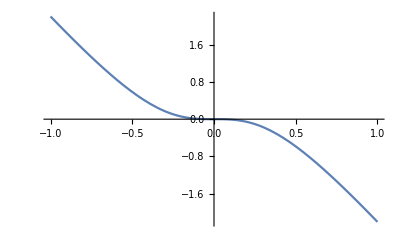

```mathematica
(* pick different values here *) 

Plot[ ( coilForce[[2]] /. K-> 1 /. L0-> 1 /. L-> 1  )  , {x,-1,1}]
```

```mathematica
(* Page 830 *) 

Clear[coilForceSeriesExpansion]
coilForceSeriesExpansion = 
PowerExpand[Normal[Series[coilForce[[2]],{x,0,5}]]]
```

-4 K (1-L0/L) x-(8 K L0 x^3)/L^3+(24 K L0 x^5)/L^5

## Chapter 14 Stuff

```mathematica
(* Page 832 *)

?EllipticK
?EllipticE
?EllipticF
?EllipticPi
```

```mathematica
(* Put in assumptions before Activate *) 

Clear[eq14pt14]
eq14pt14 = 
Inactivate[∫_0^φ 1/(√(1 - k^2 Sin[φ]^2))ⅆφ, Integrate] ;
eq14pt14  // pdConv
```

1/(√(1-k^2 sin^2(φ)))φ0φ

```mathematica
Normal[Series[EllipticF[ϕ,k],{ϕ,0,8}]]
```

ϕ+(k ϕ^3)/6+1/20 (-(2 k)/3+(3 k^2)/2) ϕ^5+1/42 ((2 k)/15-(2 k^2)/3+5/4 k (-(2 k)/3+(3 k^2)/2)) ϕ^7

```mathematica
Clear[harmonicOscillatorEnergy]
harmonicOscillatorEnergy = 
ℰ == 1/2 M D[x[t],t]^2+ 1/2 K x^2
```

ℰ==(K x^2)/2+1/2 M x'[t]^2

```mathematica
Clear[eq14pt16a]
eq14pt16a = 
(x/Subscript[x,0])^2+ (D[x[t],t]/Subscript[v,0])^2
```

x^2/x_0^2+x'[t]^2/v_0^2

```mathematica
Clear[eq14pt16b]
eq14pt16b = { 
Subscript[x,0]^2 == ((2 ℰ)/K) , 
Subscript[v,0]^2 == ((2 ℰ)/M)
} ;
eq14pt16b // TableForm
```

x_0^2==(2 ℰ)/K
v_0^2==(2 ℰ)/M

```mathematica
( PowerExpand[ApplySides[Sqrt,eq14pt16b]] /. Equal-> Rule  ) // TableForm
```

x_0→(√2 √ℰ)/(√K)
v_0→(√2 √ℰ)/(√M)

```mathematica
Clear[eq14pt1pt6]
eq14pt1pt6 = 
eq14pt16a == 
( eq14pt16a   /. ( PowerExpand[ApplySides[Sqrt,eq14pt16b]] /. Equal-> Rule  )   /. (harmonicOscillatorEnergy /. Equal-> Rule) // Expand // Simplify )
```

x^2/x_0^2+x'[t]^2/v_0^2==1

```mathematica
(* There's a large number of assumptions that need to do this integral.... redo this.... *) 

Inactivate[Integrate[( coilForce[[2]] /. x-> 𝓍 ) , {𝓍,0,x}],Integrate] // pdConv
```

-4 K 𝓍 (1-L0/(√(L^2+4 𝓍^2)))𝓍0x

```mathematica
Clear[answerToAbove]
answerToAbove = 
-2 K (x^2-1/2 L0 (-√(L^2)+√(L^2+4 x^2)))
```

-2 K (x^2-1/2 L0 (-√(L^2)+√(L^2+4 x^2)))

```mathematica
Clear[eq14pt1pt20]
eq14pt1pt20 = 
D[η[ξ],ξ] == (-ξ + β η[ξ] ( 1 - η[ξ]^2 ))/η[ξ]
```

η'[ξ]==(-ξ+β η[ξ] (1-η[ξ]^2))/η[ξ]

```mathematica
eq14pt1pt20[[2]] /. η[ξ]-> η
```

(β η (1-η^2)-ξ)/η

```mathematica
?StreamPlot
```

```mathematica
Clear[eq14pt3pt1]
eq14pt3pt1 = 
{x+ξ[t,x],η[t,x],ζ[t,x]}
```

{x+ξ[t,x],η[t,x],ζ[t,x]}

```mathematica
D[eq14pt3pt1,x] // pdConv
```

{(∂ξ(t,x))/(∂x)+1,(∂η(t,x))/(∂x),(∂ζ(t,x))/(∂x)}

```mathematica
Clear[eq14pt3pt2]
eq14pt3pt2 = 
Sqrt[D[eq14pt3pt1,x] . D[eq14pt3pt1,x]]  ;
eq14pt3pt2// pdConv
```

√(((∂ζ(t,x))/(∂x))^2+((∂η(t,x))/(∂x))^2+((∂ξ(t,x))/(∂x)+1)^2)

```mathematica
Clear[eq14pt3pt3b]
eq14pt3pt3b = 
D[eq14pt3pt1,x]/eq14pt3pt2  ;
eq14pt3pt3b// pdConv
```

{((∂ξ(t,x))/(∂x)+1)/(√(((∂ζ(t,x))/(∂x))^2+((∂η(t,x))/(∂x))^2+((∂ξ(t,x))/(∂x)+1)^2)),((∂η(t,x))/(∂x))/(√(((∂ζ(t,x))/(∂x))^2+((∂η(t,x))/(∂x))^2+((∂ξ(t,x))/(∂x)+1)^2)),((∂ζ(t,x))/(∂x))/(√(((∂ζ(t,x))/(∂x))^2+((∂η(t,x))/(∂x))^2+((∂ξ(t,x))/(∂x)+1)^2))}

## (Find place for this... ) Bessel Equations Drum Head (Taken From Documentation For New In Version 12)

```mathematica
eqn=r D[u[r,t],{t,2}]==D[r D[u[r,t],r],r];
```

```mathematica
bc=u[1,t]==0;
```

```mathematica
ic={u[r,0]==0,Derivative[0,1][u][r,0]==1};
```

```mathematica
(dsol=DSolve[{eqn,bc,ic},u[r,t],{r,t}])//TraditionalForm
```

{{u(r,t)→(2 0r 0K[1] 10K[1] sin(t 0K[1]))/(((00K[1])^2+(10K[1])^2) (0K[1])^2)K[1]1∞}}

```mathematica
h[r_,t_]=u[r,t]/.dsol[[1]]/.{∞->3}//Activate//N;
```

```mathematica
N[(2 π)/BesselJZero[0,1]]
```

2.61274

```mathematica
ListAnimate[Table[Plot3D[Evaluate[h[r,t]/.{r->Sqrt[x^2+y^2]}],{x,y}∈Disk[],PlotRange->{-1,1},Ticks->None,Mesh->True,MeshStyle->{Red,Blue},PlotStyle->Yellow,Boxed->False,Axes->False,ImageSize->Medium,AspectRatio->1,Background->Lighter[Orange,0.85]],{t,0,10.45,0.05}]]
```

## (Find place for this... ) Poisson Periodic Boundary Conditions (Taken From Documentation For New In Version 12)

```mathematica
Ω=Cuboid[{0,0,0},{5,1,1}];
ufun=NDSolveValue[{-Laplacian[u[x,y,z],{x,y,z}]==1,DirichletCondition[u[x,y,z]==0,0<x<5],PeriodicBoundaryCondition[u[x,y,z],x==0,TranslationTransform[{5,0,0}]]},u,{x,y,z}∈Ω]
```

InterpolatingFunction[{{0., 5.}, {0., 1.}, {0., 1.}}, <>]

```mathematica
SliceContourPlot3D[ufun[x,y,z],{{"XStackedPlanes",{0,1.5,3.5,5}},{"YStackedPlanes",1},{"ZStackedPlanes",1}},{x,y,z}∈Ω,ColorFunction->"TemperatureMap",Boxed->False,Axes->False]
```

## (Find place for this... ) Wave With Absorbing Boundary Conditions (Taken From Documentation For New In Version 12)

```mathematica
eqn=D[u[t,x],{t,2}]==D[u[t,x],{x,2}]+NeumannValue[-Derivative[1,0][u][t,x],x==0||x==1];
```

```mathematica
u0[x_]:=Evaluate[D[0.125 Erf[(x-0.5)/0.125],x]];
ic={u[0,x]==u0[x],Derivative[1,0][u][0,x]==0};
```

```mathematica
ufun=NDSolveValue[{eqn,ic},u,{t,0,1},{x,0,1},Method->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement"}}];
```

```mathematica
list=Table[Plot[ufun[t,x],{x,0,1},PlotRange->{-0.1,1.3}],{t,0,1,0.1}];
ListAnimate[list]
```

## (Find place for this... ) Wave Periodic Boundary Conditions

```mathematica
eqn=D[u[t,x],{t,2}]==D[u[t,x],{x,2}]+NeumannValue[-Derivative[1,0][u][t,x],x==0||x==1];
```

```mathematica
f[x_]=D[0.125 Erf[(x-0.5)/0.125],x];
vInit[x_]=-D[f[x],x];
ic={u[0,x]==f[x],Derivative[1,0][u][0,x]==vInit[x]};
```

```mathematica
bc=PeriodicBoundaryCondition[u[t,x],x==0,TranslationTransform[{1}]];
```

```mathematica
ufun=NDSolveValue[{eqn,ic,bc},u,{t,0,2},{x,0,1},Method->{"MethodOfLines"}];
```

```mathematica
plots=Table[Plot[ufun[t,x],{x,0,1},PlotRange->{-0.1,1.3}],{t,0,2,.1}];
ListAnimate[plots]
```

## (Find place for this... ) Poisson Periodic Boundary Condition (Taken From Documentation For New In Version 12)

```mathematica
Ω=RegionDifference[RegionUnion[Disk[],Rectangle[{0,-1},{2,1}]],Disk[{2,0}]];
```

```mathematica
ufun = NDSolveValue[{-∇_{x,y}^2 u[x,y] == 1, 
    PeriodicBoundaryCondition[u[x, y], (x - 2)^2 + y^2 == 1, 
     Function[x, x - {2, 0}]], 
    DirichletCondition[
     u[x, y] == 0, (0 <= x < 2 - 10^-6 && (y <= -1 || y >= 1))]}, 
   u, {x, y} ∈ Ω];
```

```mathematica
ContourPlot[ufun[x,y],{x,y}∈Ω,ColorFunction->"TemperatureMap",AspectRatio->Automatic]
```

## Axisymmetric PDE (Taken From Documentation For New In Version 10)

```mathematica
Subscript[r,1]=1;Subscript[r,2]=2;
Ω=ImplicitRegion[True,{{r,Subscript[r,1],Subscript[r,2]},{z,0,1/2}}];
```

```mathematica
k=100;nv=-100;dc=10;
uif=NDSolveValue[{k/r D[r D[u[r,z],r],r]+k D[u[r,z],{z,2}]==NeumannValue[nv,r==1],DirichletCondition[u[r,z]==10,r==2]},u,{r,z}∈Ω];
```

```mathematica
dp=DensityPlot[uif[r,z],{r,z}∈Ω,ColorFunction->"Temperature"]
```

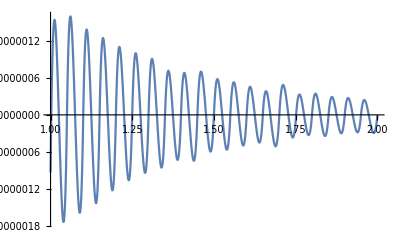

```mathematica
analyticalSolution[r_,z_]=(dc+nv*Subscript[r,1]/k Log[r/Subscript[r,2]]);
Plot[uif[r,0]-analyticalSolution[r,z],{r,Subscript[r,1],Subscript[r,2]}]
```

```mathematica
Show[RegionPlot3D[1≤x^2+y^2≤4&&0≤z≤1/2,{x,-2,2},{y,-2,2},{z,0,1/2},Boxed->False,Axes->False,PlotPoints->40,PlotStyle->{Opacity[0.2]},Mesh->False],Graphics3D[{EdgeForm[Red],FaceForm[Gray],GraphicsComplex[{{1,0,0},{2,0,0},{2,0,1/2},{1,0,1/2}},{Texture[Show[dp,Frame->False,PlotRangePadding->None]],Lighting->{{"Ambient",White}},Polygon[{{1,2,3,4}},VertexTextureCoordinates->{{{0,0},{1,0},{1,1},{0,1}}}]}]}]]
```

## 2 D Wave Animation (Taken From Documentation For New In Version 10)

```mathematica
Ω=RegionDifference[RegionUnion[Disk[],Rectangle[{0,0},{2,2}]],Disk[{1/4,1/4},1/5]]
```

BooleanRegion[(#1||#2)&&!#3&,{Disk[{0,0}],Rectangle[{0,0},{2,2}],Disk[{1/4,1/4},1/5]}]

```mathematica
uifWave = NDSolveValue[{D[u[t,x,y], t,t] - 
       Inactive[Laplacian][u[t, x, y], {x, y}] == 0, 
     u[0, x, y] == E^(-5 ((x - 3/2)^2 + (y - 3/2)^2)), 
Derivative[1,0,0][u][0, x, y] == 0, 
     DirichletCondition[u[t, x, y] == 0, True]}, 
    u, {t, 0, 2 π}, {x, y} ∈ Ω] // Quiet
```

InterpolatingFunction[{{0., 6.28319}, {-1., 2.}, {-1., 2.}}, <>]

```mathematica
framesWEQ=Table[Plot3D[uifWave[t,x,y],{x,y}∈uifWave["ElementMesh"],PlotRange->{-1,1},Boxed->False,Axes->False,Mesh->None],{t,0,2 π,2 π/50}];
```

```mathematica
Animate[framesWEQ[[i]],{{i,16,"time"},1,Length[framesWEQ],1},SaveDefinitions->True]
```

## Transient Boundary Conditions (Taken From Documentation For New In Version 10)

```mathematica
s=1/8;
Ω=ImplicitRegion[(x≤-s||x≥s||y≤-s||y≥s)&&x^2+y^2≤1,{x,y}]
```

ImplicitRegion[(x≤-1/8||x≥1/8||y≤-1/8||y≥1/8)&&x^2+y^2≤1,{x,y}]

```mathematica
Subscript[Γ,D]={DirichletCondition[u[t,x,y]==Sin[t]^2,-s≤x≤s&&-s≤y≤s],DirichletCondition[v[t,x,y]==D[Sin[t]^2,t],-s≤x≤s&&-s≤y≤s]}
```

{DirichletCondition[u[t,x,y]==Sin[t]^2,-1/8≤x≤1/8&&-1/8≤y≤1/8],DirichletCondition[v[t,x,y]==2 Cos[t] Sin[t],-1/8≤x≤1/8&&-1/8≤y≤1/8]}

```mathematica
sysSol=NDSolveValue[{D[u[t,x,y],t]==v[t,x,y],D[v[t,x,y],t]==Inactive[Laplacian][u[t,x,y],{x,y}],Subscript[Γ,D],u[0,x,y]==0,v[0,x,y]==0},u,{t,0,2 Pi},{x,y}∈Ω]
```

InterpolatingFunction[{{0., 6.28319}, {-1., 1.}, {-1., 1.}}, <>]

```mathematica
framesTFBC=Table[Plot3D[sysSol[t,x,y],{x,y}∈Ω,PlotRange->{-1,2},Boxed->False,Axes->False,Mesh->None],{t,0,2 π,2 π/50}];
```

```mathematica
Animate[framesTFBC[[i]],{{i,25,"time"},1,Length[framesTFBC],1},SaveDefinitions->True]
```

$Aborted[]

## N - Body Example From Documentation (Taken From Documentation For New In Version 9 and 12)

```mathematica
data=NBodySimulation["InverseSquare",{<|"Mass"->1,"Position"->{0,0},"Velocity"->{0,.5}|>,<|"Mass"->1,"Position"->{1,1},"Velocity"->{0,-.5}|>,<|"Mass"->1,"Position"->{0,1},"Velocity"->{0,0}|>},4]
```

NBodySimulationData[3, <4.>]

```mathematica
data[All,4]
```

{<|Mass→1,Position→{0.869387,1.03249},Velocity→{0.193378,0.789462},Momentum→{0.193378,0.789462}|>,<|Mass→1,Position→{-0.694252,-0.384878},Velocity→{-1.03984,-0.796168},Momentum→{-1.03984,-0.796168}|>,<|Mass→1,Position→{0.824865,1.35239},Velocity→{0.846463,0.00670572},Momentum→{0.846463,0.00670572}|>}

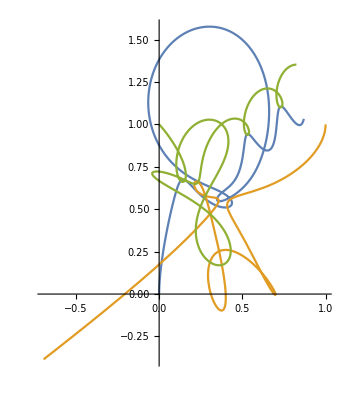

```mathematica
ParametricPlot[Evaluate[data[All,"Position",t]],{t,0,4}]
```

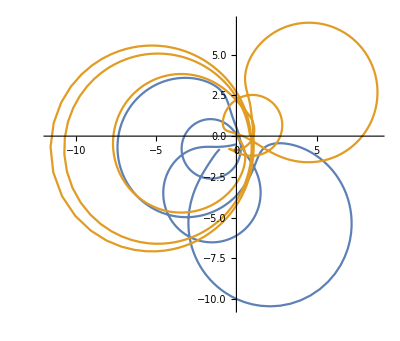

```mathematica
ParametricPlot[Evaluate[data[{2,3},"Velocity",t]],{t,0,4},PlotRange->All,PlotPoints->1000]
```

```mathematica
data2=NBodySimulation["InverseSquare",<|"b1"-><|"Mass"->1,"Position"->{0,0},"Velocity"->{0,.5}|>,"b2"-><|"Mass"->2,"Position"->{1,1},"Velocity"->{0,-.5}|>|>,2]
```

NBodySimulationData[…]

```mathematica
data4=NBodySimulation[data2,4]
```

NBodySimulationData[…]

```mathematica
data4[All,"Mass"]
```

{1,2}

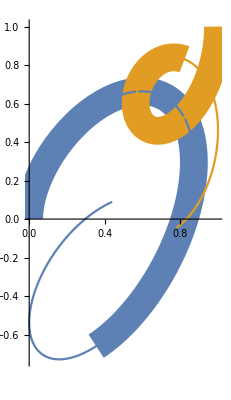

```mathematica
Show[ParametricPlot[Evaluate[data2[All,"Position",t]],{t,0,2},PlotStyle->Thickness[.05]],ParametricPlot[Evaluate[data4[All,"Position",t]],{t,0,4}],PlotRange->All]
```

```mathematica
(* 4 Body Problem Inverse Square *)
```

```mathematica
data=NBodySimulation["InverseSquare",{<|"Mass"->1,"Position"->{0,0,0},"Velocity"->{0,0,0}|>,<|"Mass"->2,"Position"->{1,1,1},"Velocity"->{0,0,0}|>,<|"Mass"->3,"Position"->{1,1,0},"Velocity"->{0,0,0}|>,<|"Mass"->4,"Position"->{0,1,1},"Velocity"->{0,0,0}|>},1];

Manipulate[ParametricPlot3D[Evaluate[data[All,"Position",t]],{t,0,k},PlotRange->{{0,1},{0,1},{0,1}}],{k,0.1,1}]
```

## Gaussian Pulse Page 876

```mathematica
Clear[gaussianPage876]
gaussianPage876 = 
2/(√(2π(2/x))) Exp[(-(t - x/c)^2 c^2)/(4/x)]
```

(ⅇ^(-1/4 c^2 x (t-x/c)^2))/(√π √(1/x))

```mathematica
PowerExpand[( gaussianPage876 /. c-> 1  )]
```

(ⅇ^(-1/4 (t-x)^2 x) √x)/(√π)

```mathematica
Manipulate[Plot[Evaluate[PowerExpand[( gaussianPage876 /. c-> 1  )]  /. t-> tmax],{x,0,50}, PlotRange->{0,4}],{tmax,0,50,1}]
```